#### Units and constants

```mathematica
$Assumptions:={m>0}
c=299792458m/s;
e=1.602 10^-19 A s;
a0=5.292 10^-11 m;
ℏ=1.055 10^-34 m^2 kg/s;
kg=(A s^3)/m^2 V;
ϵ0=8.854 10^-12(A s)/(V m);
A=W/V;
GHz=10^9 s^-1;
cm=1/(29.9792458 GHz);
kB=1.38 10^-23 m^2 kg s^-2 K^-1;
h=6.63 10^-34 m^2 kg /s;
y0=siemens/376.73;
in=0.0254m;
mil=in/1000;
mm=10^-3 m;
```

## Task #2: anti-reflective windows

See Thin-Film Optical Filters by H A Macleod for thin-film theory; I merely quote results in what follows.

#### Thin film reflectance at normal incidence

The wavelength in vacuum is

```mathematica
λ[n_,f_]:=c/f
```

The phase change for planar wavefronts at normal incidence across a window of thickness d and refractive index n will be

```mathematica
δ[n_,d_,f_]:=(2π n d)/λ[n,f]
```

The admittance of the window is given by [see eqn 2.92]

```mathematica
Y[n_,d_,f_]:=(y0 Cos[δ[n,d,f]]+ⅈ y1 Sin[δ[n,d,f]])/(Cos[δ[n,d,f]]+ⅈ(y0/y1)Sin[δ[n,d,f]])
```

where y_0 is the admittance of free space, while for an ideal dielectric window, its admittance will be y_1=√(ϵ_1/μ_1). Since for dielectrics, μ≈μ_0, we can assume y_1≈√ϵ_r y_0. For fused silica, respectively, these values are approximately

```mathematica
y1=√3.8 y0;
```

The corresponding power reflectivity is [eqn 2.91]

```mathematica
R[n_,d_,f_]:=Abs[(y0-Y[n,d,f])/(y0+Y[n,d,f])]^2
```

A 5 mm thick fused silica window would thus have the reflectivity

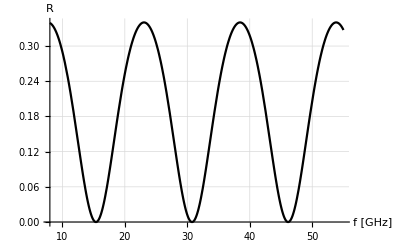

```mathematica
p1=Plot[
R[√3.8,5/1000 m,f GHz],
{f,8,55},
AxesLabel->{"f [GHz]","R"},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["AR_win_p1.pdf",p1];
```

We see that unless the window thickness is matched to the frequencies of the radiation we use, the window can reflect up to ~35% of incident power. However, when the frequency is matched, ideally no power is reflected at all. Even if we change the frequency by ~1.6 GHz from each minimum, the reflectivity will stay below ~5%.

#### Half-wave windows

Due to the periodicity of the reflection coefficient, we only need a single window thicknesses to cover our four frequencies (13.3797 GHz, 26.7595 GHz, 40.1392 GHz, 53.519 GHz), namely, in millimeters,

```mathematica
soln=FindRoot[R[√3.8,d/1000 m,13.3797 GHz],{d,6}]
```

{d→5.74715}

It’s a well known fact that half-wave layers have no effect on reflectance or transmittance of assemblies, at wavelengths at which they are truly half-wave. So we can have a window twice as thick:

```mathematica
th0=Round[2d/.soln,0.001]
```

11.494

#### Residual reflectivity

We have the frequencies (in GHz):

```mathematica
f1=13.379747173774135;
f2=26.75949434754827;
f3=40.139241521322404;
```

The lower bound for reflectivity is realistically set by how precisely the window thickness can be controlled. It can be kept below 1% if the window thickness can be within about ±2mil:

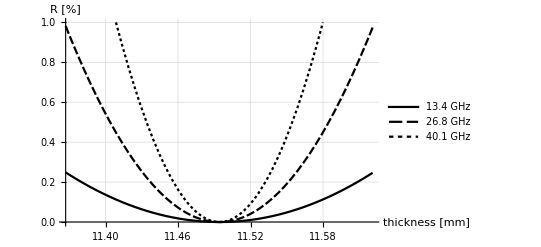

```mathematica
Δ=5*.0254;
p2=Plot[
{100R[√3.8,th/1000m,f1 GHz],100R[√3.8,th/1000m,f2 GHz],100R[√3.8,th/1000m,f3 GHz]},
{th,th0-Δ,th0+Δ},
AxesLabel->{"thickness [mm]","R [%]"},
PlotRange->{Automatic,{0,1}},
PlotLegends->{"13.4 GHz","26.8 GHz","40.1 GHz"},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["AR_win_p2.pdf",p2];
```

/home/jk/temp/thesis/figs/mathematica

Of course, this assumes a particular value of the refractive index. According to Goldsmith Table 5.1, fused silica is 1.812 ± 0.003 at 94.3 GHz, but 1.949 at 105.3 GHz. Whatever the material used, its refractive index better be known precisely to determine the exact optical thickness of the window:

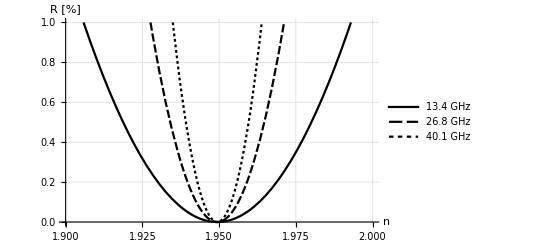

/home/jk/temp/thesis/figs/mathematica

```mathematica
p3=Plot[
{100R[n,th0/1000m,f1 GHz],100R[n,th0/1000m,f2 GHz],100R[n,th0/1000m,f3 GHz]},
{n,1.9,2},
AxesLabel->{"n","R [%]"},
PlotRange->{Automatic,{0,1}},
PlotLegends->{"13.4 GHz","26.8 GHz","40.1 GHz"},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
SetDirectory[NotebookDirectory[]]
Export["AR_win_p3.pdf",p3];
```

The frequency bandwidth to keep R below 1% is about 300 MHz:

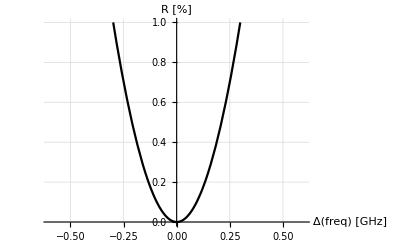

/home/jk/temp/thesis/figs/mathematica

```mathematica
p4=Plot[
100R[√3.8,th0/1000m,(f1+Δf) GHz],{Δf,-.6,.6},
AxesLabel->{"Δ(freq) [GHz]","R [%]"},
PlotRange->{Automatic,{0,1}},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
SetDirectory[NotebookDirectory[]]
Export["AR_win_p4.pdf",p4];
```

#### The effect of oblique incidence

The phase change for planar wavefronts at normal incidence across a window of thickness d and refractive index n will be

```mathematica
δ2[n_,d_,f_,θ_]:=(2π n d Cos[θ])/λ[n,f]
```

The admittance of the window is given by [see eqn 2.92]

```mathematica
Y2[n_,d_,f_,θ_]:=y0(Cos[δ2[n,d,f,θ]]+ⅈ n Sin[δ2[n,d,f,θ]])/(Cos[δ2[n,d,f,θ]]+ⅈ(1/n)Sin[δ2[n,d,f,θ]])
```

where y_0 is the admittance of free space, while for an ideal dielectric window, its admittance will be y_1=√(ϵ_1/μ_1). Since for dielectrics, μ≈μ_0, we can assume y_1≈√ϵ_r y_0. For fused silica, ϵ_r≈3.8.

The corresponding power reflectivity is [eqn 2.91]

```mathematica
R2[n_,d_,f_,θ_]:=Abs[(y0-Y2[n,d,f,θ])/(y0+Y2[n,d,f,θ])]^2
```

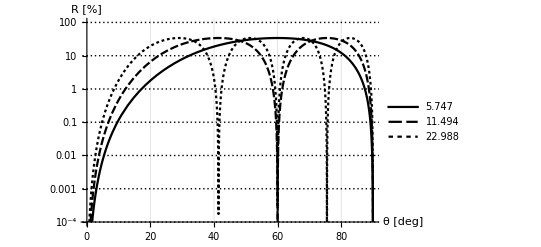

/home/jk/temp/thesis/figs/mathematica

```mathematica
p5=LogPlot[
{
100R2[√3.8,(th0/1000m)/2,f1 GHz,θ/(180/π)],
100R2[√3.8,(th0/1000m)/1,f1 GHz,θ/(180/π)],
100R2[√3.8,(th0/1000m)/(.5),f1 GHz,θ/(180/π)]
},
{θ,0,90},
AxesLabel->{"θ [deg]","R [%]"},
PlotLegends->{th0/2,th0,2th0},
PlotRange->{Automatic,{10^-4,100}},
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic
]
SetDirectory[NotebookDirectory[]]
Export["AR_win_p5.pdf",p5];
```

#### Estimate the angle of incidence

The radius of curvature, beam waist, and intensity are

```mathematica
R[z_,w0_,f_]:=z+1/z((π w0^2)/(c/f))^2
w[z_,w0_,f_]:=w0 √(1+(((c/f) z)/(π w0^2))^2)
I0[r_,z_,w0_,f_]:=(w0/w[z,w0,f])^2 Exp[-(2 r^2)/w[z,w0,f]^2]
```

For the 13.4 GH beam, the radius of curvature is

```mathematica
z1=7.30in;
w1=1in;
R1=R[z1,w1,f1 GHz];
```

We can plot the beam intensity as a function of the angle of incidence:

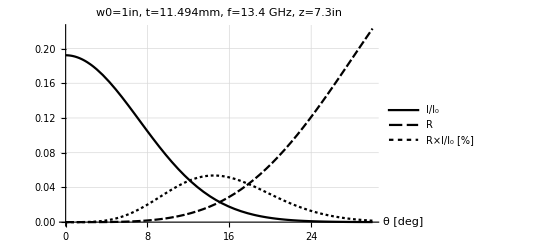

/home/jk/temp/thesis/figs/mathematica

```mathematica
p6=Plot[
{
I0[R1 Cos[(90-θ)/(180/π)],z1,w1,f1 GHz],
R2[√3.8,(th0/1000m)/1,f1 GHz,θ/(180/π)],
100I0[R1 Cos[(90-θ)/(180/π)],z1,w1,f1 GHz]
R2[√3.8,(th0/1000m)/1,f1 GHz,θ/(180/π)]
},
{θ,0,30},
AxesLabel->{"θ [deg]",""},
PlotLegends->{"I/I_0","R","R×I/I_0 [%]"},
PlotRange->All,
PlotTheme->"Monochrome",
BaseStyle->FontSize->16,
GridLines->Automatic,
PlotLabel->Style["w0=1in, t=11.494mm, f=13.4 GHz, z=7.3in",14]
]
SetDirectory[NotebookDirectory[]]
Export["AR_win_p6.pdf",p6];
```